```mathematica
Collatz[n_]:=If[EvenQ[n],n/2,3n+1];
```

```mathematica
Collatz[1]=1;
```

```mathematica
DoCollatz[n_]:=
			
			FixedPointList[Collatz,n]//(Print[Length[#]];#)&
```

```mathematica
DoCollatz[4]
```

4

{4,2,1,1}

951

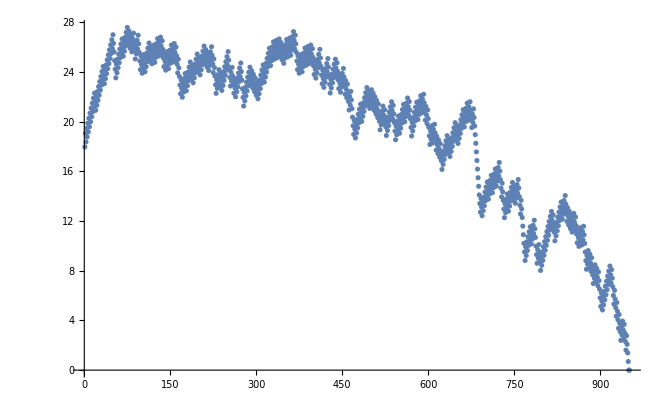

```mathematica
ListPlot[Log/@DoCollatz@63728127]
```

```mathematica
Table[Length[DoCollatz[n]],{n,1,100}]
```

2

3

9

4

7

10

18

5

21

8

16

11

11

19

19

6

14

22

22

9

9

17

17

12

25

12

113

20

20

20

108

7

28

15

15

23

23

23

36

10

111

10

31

18

18

18

106

13

26

26

26

13

13

114

114

21

34

21

34

21

21

109

109

8

29

29

29

16

16

16

104

24

117

24

16

24

24

37

37

11

24

112

112

11

11

32

32

19

32

19

94

19

19

107

107

14

120

27

27

27

{2,3,9,4,7,10,18,5,21,8,16,11,11,19,19,6,14,22,22,9,9,17,17,12,25,12,113,20,20,20,108,7,28,15,15,23,23,23,36,10,111,10,31,18,18,18,106,13,26,26,26,13,13,114,114,21,34,21,34,21,21,109,109,8,29,29,29,16,16,16,104,24,117,24,16,24,24,37,37,11,24,112,112,11,11,32,32,19,32,19,94,19,19,107,107,14,120,27,27,27}

```mathematica
ReverseCollatz[n_]:=
	Switch[Mod[n,6],
		0,n,
		1,2n,
		2,2n,
		3,n,
		4,(n-1)/3,
		5,2n]
```

```mathematica
FixedPointList[ReverseCollatz,976]
```

{976,325,650,1300,433,866,1732,577,1154,2308,769,1538,3076,1025,2050,683,1366,455,910,303,303}

```mathematica
DoCollatz[9]
```

21

{9,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1,1}

```mathematica
Collatz[1]=1;
Collatz[n_]:=Collatz[n]=If[EvenQ[n],n/2,3n+1];

CountCollatz[{1,m_}]:=m;
CountCollatz[{n_,m_}]:=CountCollatz[{Collatz[n],m+1}]
```

```mathematica
CountCollatz[{27,0}]
```

111

```mathematica
Table[CountCollatz[{i,0}],{i,2,20000}]
```

{1,7,2,5,8,16,3,19,6,14,9,9,17,17,4,12,20,20,7,7,15,15,10,23,10,111,18,18,18,106,5,26,13,13,21,21,21,34,8,109,8,29,16,16,16,104,11,24,24,24,11,11,112,112,19,32,19,32,19,19,107,107,6,27,27,27,14,14,«19863»,105,74,74,136,74,92,92,118,118,118,74,136,118,136,118,167,167,167,211,136,136,43,43,136,136,74,74,74,74,74,74,74,74,167,167,43,211,92,92,167,167,167,167,92,167,92,167,92,92,167,167,180,92,74,74,180,180,66,66,180,66,180,66,92,92,92,66,30}

```mathematica
Max[%]
```

278

```mathematica
63728127
```